Mathematica Assignment #1

If you need help and can’t find it with Google, there are resources at:
https://dornsife.usc.edu/mathcenter/mathematica/.

Due by 9am, Friday 10/28.  Submit your file using Blackboard.

1. Look at the help documentation for the functions Derivative and D, using the commands ?Derivative and ?D, and clicking on the >>.  Look over some of the examples of how to use these functions.  Using these functions, or some other methods, calculate the following derivatives.  Do you agree with the answers that Mathematica gives?

a)  x^2-4x+1
b)  x^2 sin(x)
c)  x^3 sin(x^2)
d)  x^π tan(x^125)
e) (√(sin(x)))/x^2

2. Come up with a horribly complicated function that you could, in theory, take the derivative of using things we’ve learned so far in class.  But something so hideous it would take forever to do by hand.  Be creative.  Then use Mathematica to calculate the derivative.

3. The following code plots a function and its first and second derivative on the same axis.  Experiment by changing f(x) to some other functions.  Which color curve is f(x), which is its derivative, and which is its second derivative?

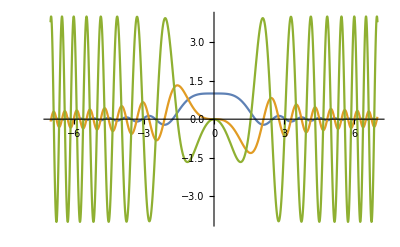

```mathematica
f[x_]:= Sin[x^2]/x^2;
Plot[{f[x], f'[x], f''[x]}, {x,-7,7}, ImageSize->Full]
```

4. The following code plots a generic cubic function and its derivative.  The four slider bars allow you to change the coefficients of the cubic (and the last one changes the window size, i.e. zooms in and out).  Play around with the coefficients and pay attention to the relationship between the two graphs.  Find values for the coefficients so that the cubic looks like it has a critical point (derivative is zero) but not a max or min.  What can you say about the derivative graph in this situation?

```mathematica
Manipulate[Plot[{a x^3+b x^2 + c x + d, 3a x^2+2b x+c}, {x,-z,z}, ImageSize->Full], {a,-3,3},{b,-3,3},{c,-6,6},{d,-3,3},{z,2,7}]
```

5. Let g(x) be defined as below.  Use the Limit function to calculate the limit of g(x):

a) As x approaches 5.
b) As x approaches 2.
c) As x approaches 0.
d) As x goes to negative infinity.

```mathematica
g[x_] := (x^2-6x+5)/(x^2-5x);
```

6. Experiment with the functions Factor, Simplify, and Solve.  Give (your own) examples of the computational power of each.

7. Factor the polynomial x^n - 1 for a bunch of different n values.  Do you notice a pattern?  What happens when n is prime?  Hunt online (e.g. on Wikipedia) for more details on this phenomenon, and see if you can make sense of it.

8. Find a new cool Mathematica function, and give three (of your own) examples of how to use it (e.g. 3D plotting? prime numbers? roots of polynomials? infinite sums?)

9. Find something else cool that you can do with Mathematica, or Wolfram|Alpha, or some other Wolfram thing.